{-9.23428,{x→0.336344,y→-2.3451}}

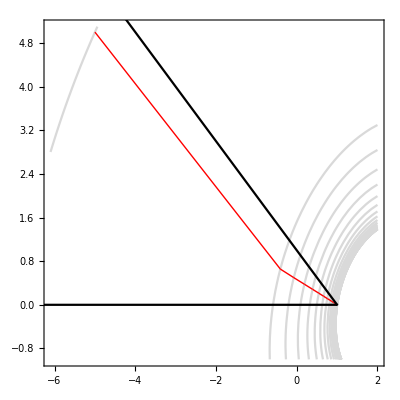

{26,7014}

{0.999566,0.000223393}

```mathematica
Ogr1=ContourPlot[{x+10==0,y==0,x+y==1},{x,-10.01,1.01},{y,-0.01,11.01},ContourStyle->{Black,Black,Black}];
Ogr2=ContourPlot[(x+3)^2/16+(y+4)^2/9==1,{x,-10,1.01},{y,-10,1},ContourStyle->Black];
F1[x_,y_]:=10 x^2-4x y+7 y^2-4 √5(5x-y)-16;
F2[x_,y_]:=(x^2-y)^2+(x-1)^2;
F3[x_,y_]:=5*(x^2-y)^2+(x-1)^2;
FindMinimum[{F1[x,y],x>=-10&&y>=0&&x+y<=1},{x,y}];
FindMinimum[{F2[x,y],x>=-10&&y>=0&&x+y<=1},{x,y}];
FindMinimum[{F3[x,y],x>=-10&&y>=0&&x+y<=1},{x,y}];
FindMinimum[{F1[x,y],(x+3)^2/16+(y+4)^2/9==1},{x,y}]
FindMinimum[{F2[x,y],(x+3)^2/16+(y+4)^2/9==1},{x,y}];
FindMinimum[{F3[x,y],(x+3)^2/16+(y+4)^2/9==1},{x,y}];
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f1Ogr1p1.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-6.1,2},{y,-1,5.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

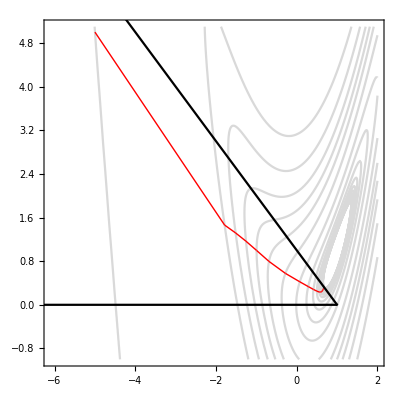

{25,6450}

{0.677671,0.320524}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f2Ogr1p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-6.1,2},{y,-1,5.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

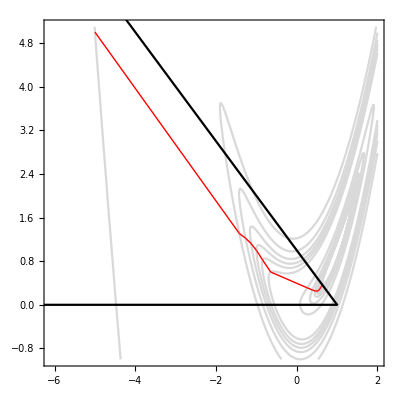

{24,33308}

{0.630719,0.366679}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f3Ogr1p1.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-6.1,2},{y,-1,5.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

{{26,8120},{-6,-4},{-0.484781,-2.97049},{-0.26001,-2.8222},{-0.0947332,-2.70042},{0.0265485,-2.60642},{0.114435,-2.53493},{0.17803,-2.48221},{0.223643,-2.4435},{0.256496,-2.41566},{0.279051,-2.39466},{0.29529,-2.3798},{0.306526,-2.36891},{0.313845,-2.36038},{0.318145,-2.35332},{0.318879,-2.34568},{0.320943,-2.34206},{0.318783,-2.33542},{0.313499,-2.32654},{0.308026,-2.31838},{0.304607,-2.31317},{0.303724,-2.31129},{0.30395,-2.31072},{0.303977,-2.31034},{0.304731,-2.3108},{0.304794,-2.31056},{0.304893,-2.31046},{0.30503,-2.3105},{0.30503,-2.3105}}

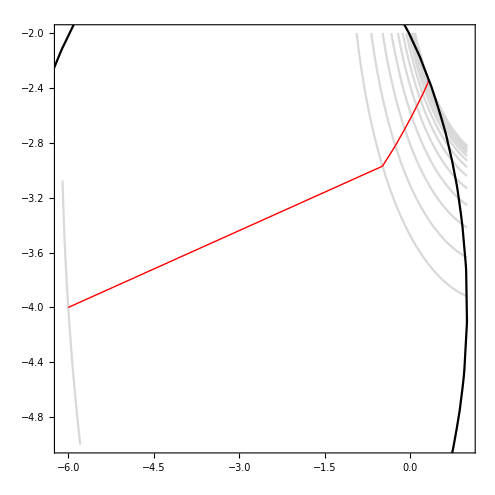

{26,8120}

{0.320943,-2.34206}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f1Ogr2p1.txt","Table"]
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-6.1,1},{y,-5,-2},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]-12}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-13}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]-12]]
```

{{21,7158},{-6,-4},{-0.865636,-3.45078},{-0.661895,-3.25844},{-0.504109,-3.04126},{-0.389343,-2.82154},{-0.308168,-2.62124},{-0.250976,-2.45218},{-0.210123,-2.31742},{-0.180868,-2.21341},{-0.15999,-2.13522},{-0.144744,-2.07751},{-0.133978,-2.03515},{-0.126272,-2.00448},{-0.120631,-1.98262},{-0.115671,-1.96764},{-0.112701,-1.95656},{-0.111076,-1.94832},{-0.10777,-1.94415},{-0.103865,-1.94237},{-0.0987736,-1.94298},{-0.0960701,-1.94269},{-0.0952882,-1.94168},{-0.0910479,-1.94383}}

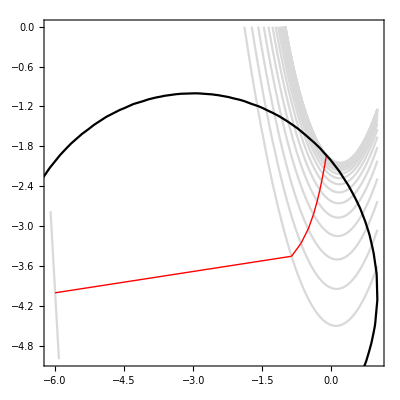

{21,7158}

{-0.0910479,-1.94383}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f2Ogr2p1.txt","Table"]
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-6.1,1},{y,-5,0},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]]]
```

{{29,18246},{-6,-4},{-0.573169,-2.8821},{-0.479759,-2.66474},{-0.419008,-2.46416},{-0.377307,-2.29954},{-0.348651,-2.16972},{-0.328445,-2.07062},{-0.31423,-1.99633},{-0.303971,-1.9417},{-0.297022,-1.90161},{-0.291796,-1.87285},{-0.288383,-1.85194},{-0.283398,-1.83879},{-0.282885,-1.82734},{-0.278268,-1.82209},{-0.27636,-1.81742},{-0.271534,-1.81656},{-0.279406,-1.80809},{-0.270512,-1.8122},{-0.265564,-1.81416},{-0.238521,-1.83223},{-0.22954,-1.83793},{-0.241853,-1.8286},{-0.227267,-1.8387},{-0.151103,-1.89483},{-0.112609,-1.92436},{-0.097758,-1.93592},{-0.0981033,-1.93557},{-0.0970043,-1.93637},{-0.0957327,-1.93735},{-0.0957327,-1.93735}}

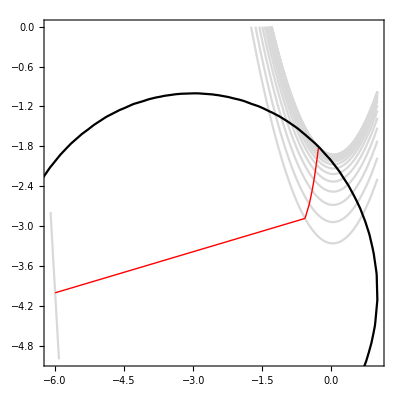

{29,18246}

{-0.279406,-1.80809}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f3Ogr2p1.txt","Table"]
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-6.1,1},{y,-5,0},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]-13}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-14}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]-13]]
```

{{22,6022},{-9,2},{0.388789,0.285003},{0.547411,0.212296},{0.666234,0.157162},{0.756044,0.115195},{0.822541,0.083981},{0.87185,0.0607847},{0.907868,0.043804},{0.93408,0.0313463},{0.953047,0.0223464},{0.966512,0.0159583},{0.976218,0.0113356},{0.983154,0.0080868},{0.987803,0.00583017},{0.99129,0.0041377},{0.994022,0.00289994},{0.995766,0.00205371},{0.996928,0.00148955},{0.997839,0.00107696},{0.998362,0.000852426},{0.998671,0.000643311},{0.999195,0.000418777},{0.999252,0.000361232},{0.999252,0.000361232}}

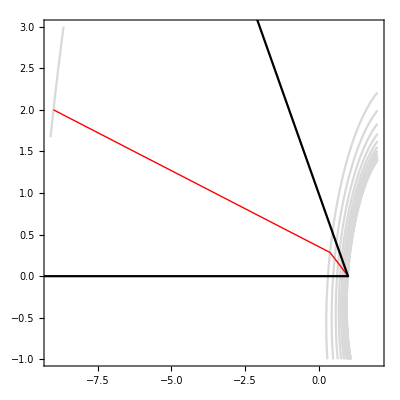

{22,6022}

{0.994022,0.00289994}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f1Ogr1p2.txt","Table"]
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-9.1,2},{y,-1,3},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]-8}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-9}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]-8]]
```

{{17,3980},{-9,2},{-1.78814,1.46683},{-1.51465,1.31772},{-1.25797,1.16629},{-0.995011,0.996628},{-0.688252,0.796018},{-0.281269,0.576514},{0.0756398,0.421737},{0.284349,0.334724},{0.414417,0.281801},{0.500023,0.250016},{0.556735,0.234568},{0.59431,0.233472},{0.619421,0.243047},{0.636603,0.258157},{0.648568,0.273402},{0.657025,0.286175},{0.663136,0.295911},{0.667327,0.303382}}

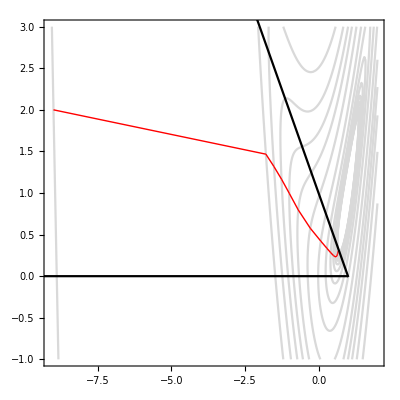

{17,3980}

{0.667327,0.303382}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f2Ogr1p2.txt","Table"]
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-9.1,2},{y,-1,3},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

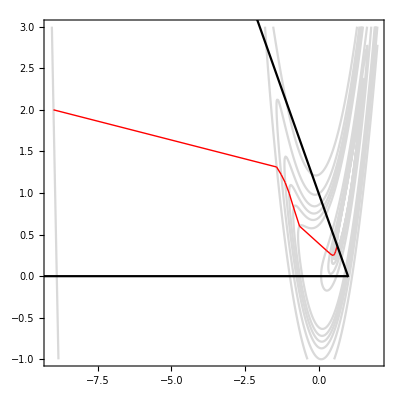

{18,5956}

{0.624418,0.356457}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f3Ogr1p2.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-9.1,2},{y,-1,3},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

{{24,11068},{0,-3},{0.0226778,-2.60167},{0.114481,-2.5349},{0.178249,-2.48235},{0.223344,-2.44313},{0.256025,-2.41511},{0.280206,-2.39593},{0.296445,-2.38108},{0.308617,-2.37132},{0.319436,-2.36689},{0.326089,-2.36248},{0.333021,-2.36194},{0.339447,-2.36328},{0.346011,-2.36655},{0.353986,-2.37274},{0.361772,-2.37962},{0.374075,-2.39253},{0.398003,-2.42004},{0.40461,-2.42725},{0.403245,-2.42498},{0.40778,-2.43012},{0.407843,-2.42988},{0.410997,-2.43363},{0.410715,-2.43305},{0.41106,-2.4334},{0.41106,-2.4334}}

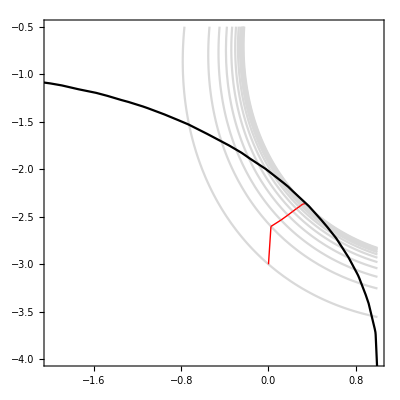

{24,11068}

{0.333021,-2.36194}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f1Ogr2p2.txt","Table"]
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-2,1},{y,-4,-0.5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]-14}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-15}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]-14]]
```

{{20,4694},{0,-3},{-0.864612,-3.45582},{-0.661849,-3.2584},{-0.504063,-3.04123},{-0.389433,-2.82147},{-0.308294,-2.62104},{-0.250893,-2.45229},{-0.210249,-2.31722},{-0.180958,-2.21335},{-0.159943,-2.13519},{-0.144698,-2.07748},{-0.133895,-2.03526},{-0.126225,-2.00445},{-0.120527,-1.98264},{-0.118476,-1.96546},{-0.115679,-1.9542},{-0.115383,-1.94493},{-0.114966,-1.93847},{-0.10565,-1.94101},{-0.111804,-1.93266},{-0.117363,-1.9259},{-0.124729,-1.91854}}

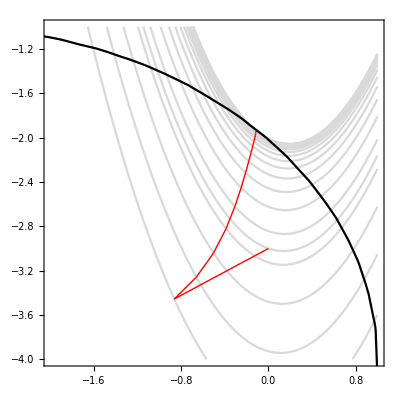

{20,4694}

{-0.10565,-1.94101}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f2Ogr2p2.txt","Table"]
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-2,1},{y,-4,-1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]-3}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-4}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]-3]]
```

{{29,17756},{0,-3},{-0.572145,-2.88714},{-0.479812,-2.66481},{-0.418925,-2.46426},{-0.377224,-2.29965},{-0.348568,-2.16983},{-0.328362,-2.07073},{-0.31432,-1.99626},{-0.304233,-1.94146},{-0.297305,-1.90145},{-0.292,-1.87267},{-0.28718,-1.85277},{-0.284666,-1.83794},{-0.281488,-1.82826},{-0.278666,-1.82181},{-0.274733,-1.81857},{-0.271932,-1.81629},{-0.273786,-1.81204},{-0.263039,-1.81741},{-0.252941,-1.82302},{-0.240019,-1.83116},{-0.223517,-1.84228},{-0.202337,-1.85718},{-0.181974,-1.87186},{-0.142773,-1.90119},{-0.129303,-1.91137},{-0.129821,-1.91086},{-0.151899,-1.89386},{-0.129067,-1.91131},{-0.128586,-1.91169},{-0.128586,-1.91169}}

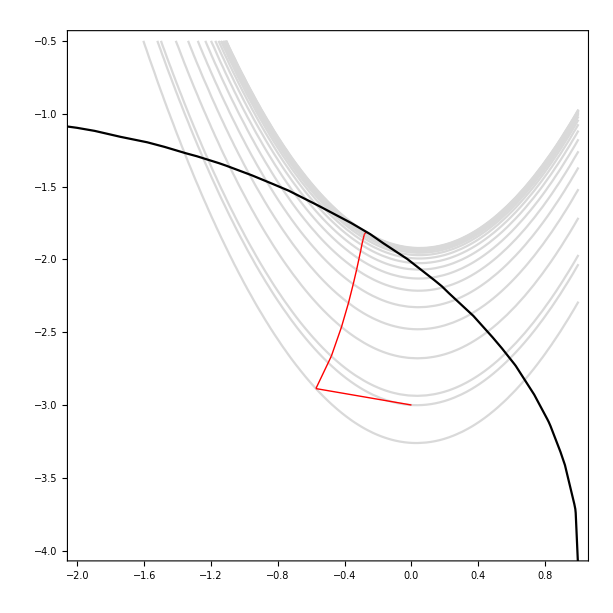

{29,17756}

{-0.273786,-1.81204}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnutreps1f3Ogr2p2.txt","Table"]
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-2,1},{y,-4,-0.5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]-13}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-14}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]-13]]
```

{{2,393},{0,10},{1.00507,0.000715284},{0.999521,0.000178535},{0.999521,0.000178535}}

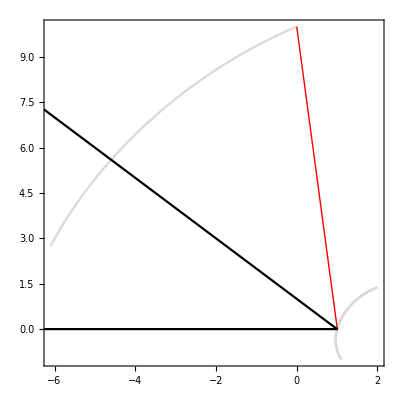

{2,393}

{0.999521,0.000178535}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f1Ogr1p1.txt","Table"]
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-6.1,2},{y,-1,10},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

{{2,466},{0,10},{0.669564,0.317079},{0.677905,0.321795},{0.677905,0.321795}}

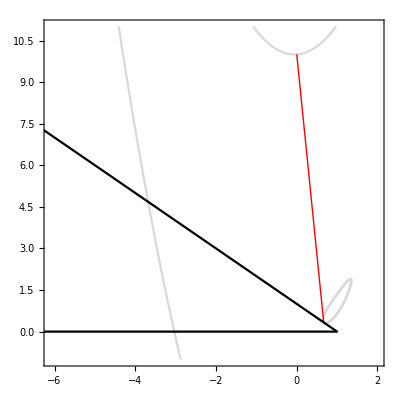

{2,466}

{0.677905,0.321795}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f2Ogr1p1.txt","Table"]
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-6.1,2},{y,-1,11},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

{{2,710},{0,10},{0.62537,0.361273},{0.63233,0.36737},{0.63233,0.36737}}

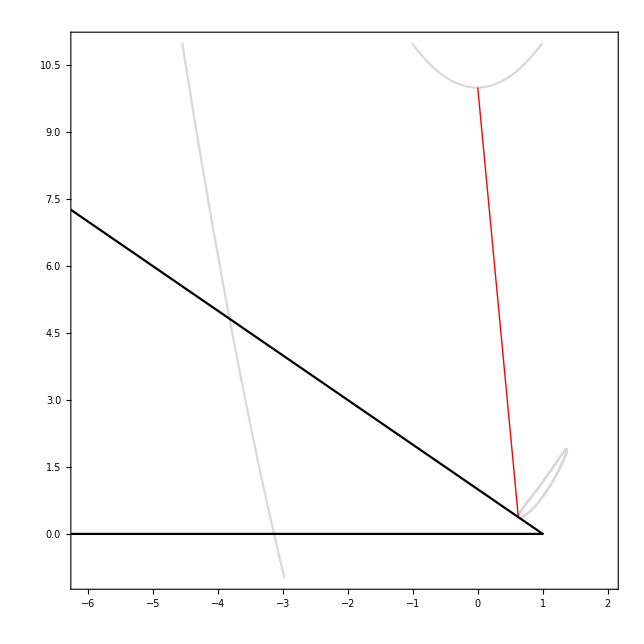

{2,710}

{0.63233,0.36737}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f3Ogr1p1.txt","Table"]
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-6.1,2},{y,-1,11},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

{{2,710},{0,10},{0.62537,0.361273},{0.63233,0.36737},{0.63233,0.36737}}

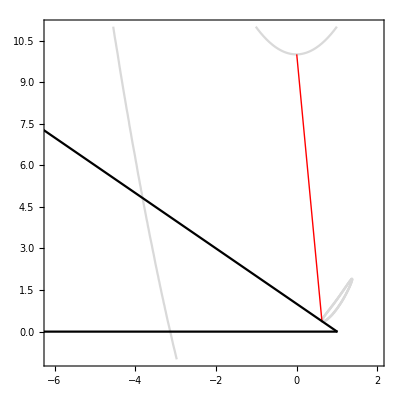

{2,710}

{0.63233,0.36737}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f3Ogr1p1.txt","Table"]
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-6.1,2},{y,-1,11},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

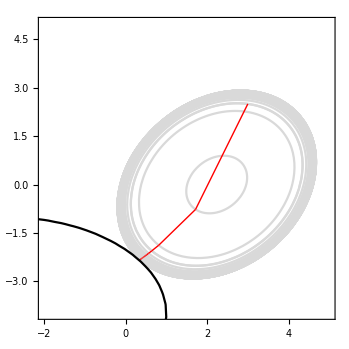

{60,8115}

{0.349609,-2.32954}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f1Ogr2p1.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-2,5},{y,-4,5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]]]
```

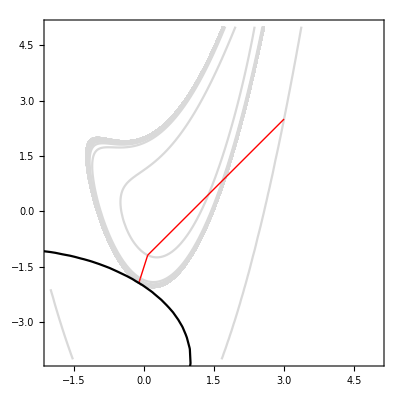

{75,24304}

{-0.09732,-1.93345}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f2Ogr2p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-2,5},{y,-4,5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]]]
```

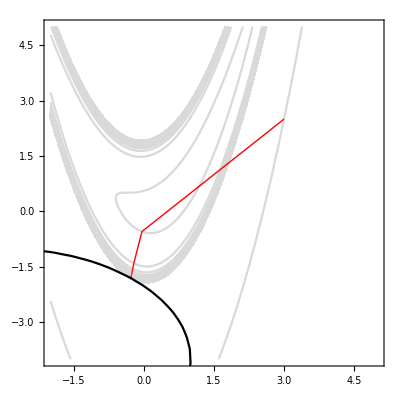

{169,40098}

{-0.280395,-1.79542}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f3Ogr2p1.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-2,5},{y,-4,5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]]]
```

{{2,419},{3,-5},{0.979221,0.00609463},{0.999617,0.000250395},{0.999617,0.000250395}}

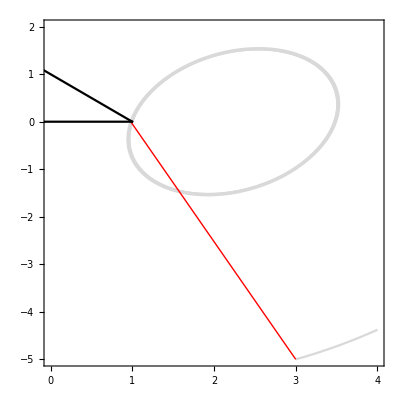

{2,419}

{0.999617,0.000250395}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f1Ogr1p2.txt","Table"]
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,0,4},{y,-5,2},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

{{2,364},{3,-5},{0.669862,0.315454},{0.677656,0.322212},{0.677656,0.322212}}

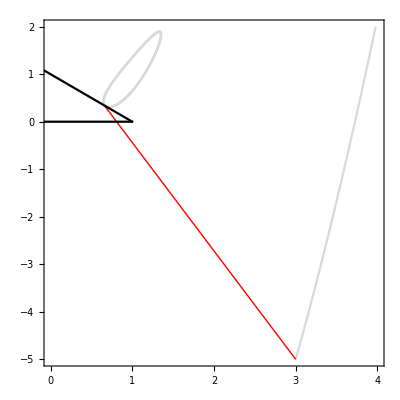

{2,364}

{0.677656,0.322212}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f2Ogr1p2.txt","Table"]
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0,4},{y,-5,2},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

{{2,366},{3,-5},{0.625668,0.359648},{0.632426,0.367442},{0.632426,0.367442}}

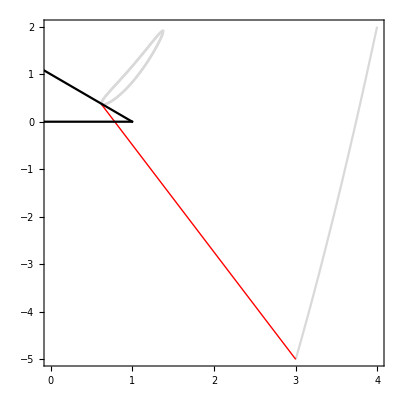

{2,366}

{0.632426,0.367442}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f3Ogr1p2.txt","Table"]
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0,4},{y,-5,2},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr1]
str[[1]]
str[[Length[str]]]
```

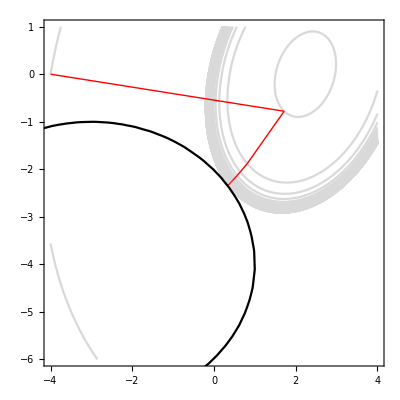

{61,8742}

{0.349315,-2.3297}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f1Ogr2p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-4,4},{y,-6,1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]]]
```

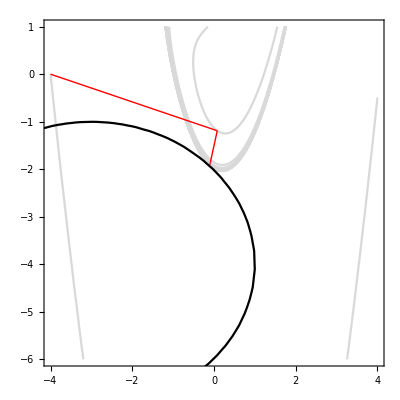

{18,2837}

{-0.108132,-1.91731}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f2Ogr2p2.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-4,4},{y,-6,1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]]]
```

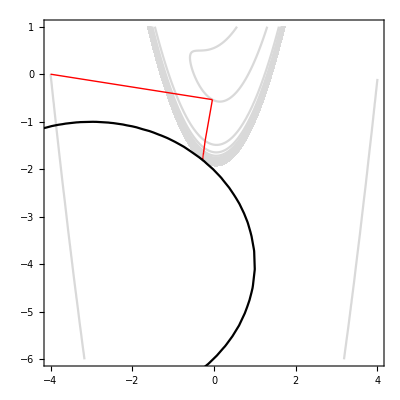

{185,48058}

{-0.281615,-1.79495}

```mathematica
str=Import["D:/1/MOVI lab/lab8/Vnesheps1f3Ogr2p2.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-4,4},{y,-6,1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,Ogr2]
str[[1]]
str[[Length[str]]]
```

```mathematica
FindMinimum[{F1[x,y],x>=-10&&y>=0&&x+y<=1},{x,y}];
FindMinimum[{F2[x,y],x>=-10&&y>=0&&x+y<=1},{x,y}];
FindMinimum[{F3[x,y],x>=-10&&y>=0&&x+y<=1},{x,y}]
FindMinimum[{F1[x,y],(x+3)^2/16+(y+4)^2/9==1},{x,y}];
FindMinimum[{F2[x,y],(x+3)^2/16+(y+4)^2/9==1},{x,y}];
FindMinimum[{F3[x,y],(x+3)^2/16+(y+4)^2/9==1},{x,y}]
F3[-0.27975,-1.80061]
```

{0.140356,{x→0.632455,y→0.367544}}

{19.2872,{x→-0.279734,y→-1.80055}}

19.2885